The goal of this notebook is to study the effect of total number of disks N on the length distribution.

```mathematica
J=1
A =1
 gamma= 1
vibration = 1
Timing[Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^N l^3×(l-1)^2/(l!)×ⅇ^(-u×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))-1,{u,-3},MaxIterations->10000],{N,{5000,8000,10000,15000, 20000}},{x,0.01,15,0.1}]]
```

1

1

1

«1 more identical outputs»

General::munfl: 175.883/(203929827411891162469297604499861487470751456486742359827810683408539939446775513496«143»5154182397262875200268932124981878786621440000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (176.876 89)/(314072098062416037868220893164838362402594800436966192929957494404364935416204309038«147»7707435274785196699124005923162587377172480000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (177.87 32041)/(196791295203948641007469847239224421114217850057794277166052766843886981233085295957«152»2479447490854773711963133521399878873251840000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{18474.5,{{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352},{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352},{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352},{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352},{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352}}}

```mathematica
J05 = Jkrj[[1]];
J1 = Jkrj[[2]];
J105 = Jkrj[[3]];
J2 = Jkrj[[4]];
J205=Jkrj[[5]];
```

```mathematica
x= Range[0.01,15,0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91}

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

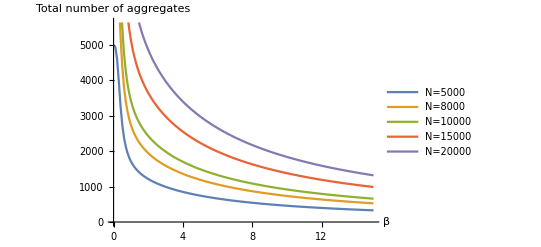

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^5000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^5000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))×5000,(ⅇ^-J1+gamma×∑_(l=2)^8000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^8000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))×8000,(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J2+gamma×∑_(l=2)^15000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^15000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))×15000,
(ⅇ^-J205+gamma×∑_(l=2)^20000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^20000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))×20000},DataRange->{0,15},PlotLegends->{"N=5000","N=8000","N=10000","N=15000","N=20000"},AxesLabel->{"β","Total number of aggregates"}]
```

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

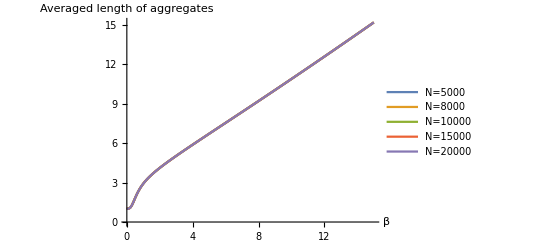

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^5000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^5000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)])),(ⅇ^-J1+gamma×∑_(l=2)^8000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^8000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)])),(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)])),(ⅇ^-J2+gamma×∑_(l=2)^15000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^15000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)])),
(ⅇ^-J205+gamma×∑_(l=2)^20000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^20000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-gamma x Cos[(n π)/(2 l)]))},DataRange->{0,15},PlotLegends->{"N=5000","N=8000","N=10000","N=15000","N=20000"},AxesLabel->{"β","Averaged length of aggregates"}]
```